```mathematica
data = Import["E:\\Alessio\\Desktop\\Computazionale\\es13\\data.txt","Table"];
```

```mathematica
data1= Take[data][[All, {1,2}]];
data2 = Take[data][[All, {1,3}]];
scarto1= Take[data][[All, {1,4}]];
scarto2 = Take[data][[All, {1,5}]];
```

1/2 (-2+π)

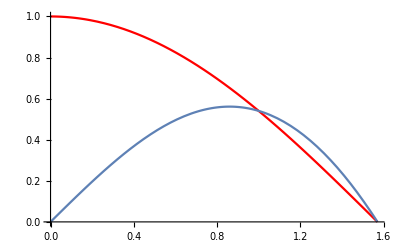

```mathematica
f1 = x*Cos[x];
Integrate[f1, {x,0,Pi/2}]
Show[Plot[Cos[x], {x,0,Pi/2},PlotStyle->Red],Plot[f1,{x,0,Pi/2}]]
```

π

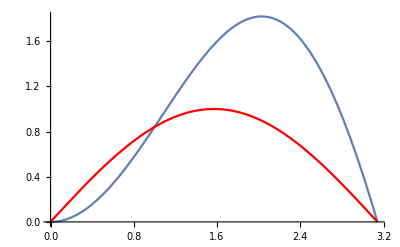

```mathematica
f2 = x*Sin[x];
Integrate[f2, {x,0,Pi}]
Show[Plot[f2,{x,0,Pi}], Plot[Sin[x], {x,0,Pi},PlotStyle->Red]]
```

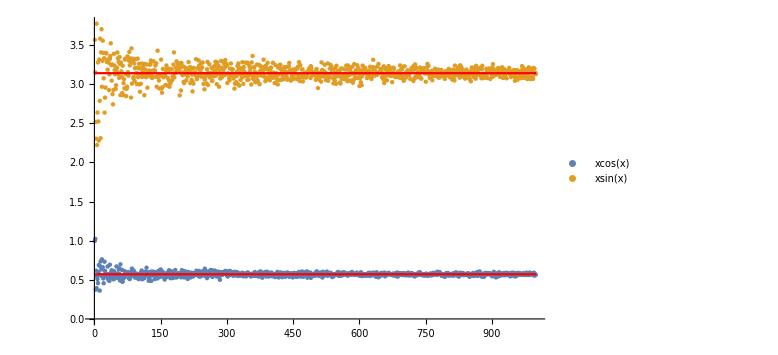

```mathematica
Show[ListPlot[{data1,data2},PlotLegends->{"xcos(x)","xsin(x)"},ImageSize->Large],Plot[{Pi,Pi/2 - 1},{x,0,1000},PlotStyle->Red ]]
```

```mathematica
Pi/2 - 1
```

-1+π/2

```mathematica
Integrate[x*Cos[x],{x,0,Pi/2}]
```

1/2 (-2+π)

```mathematica
Integrate[x*Sin[x],{x,0,Pi}]
```

π